#### Задание 21

Многокритериальная задача линейной оптимизации
А) Найти компромиссное решение. 
Б) Решить методом последовательных уступок I (метод главного критерия). Уступка по первому критерию составляет 7 % от его оптимального значения в тех вариантах заданий, где она не указана в явном виде. 
В) Решить методом последовательных уступок II (случай двух критериев). Уступка по первому критерию составляет 5, 10 и 15%, по второму критерию 10, 15 и 20% от соответствующих оптимальных значений. 
Г) Решить методом равных отклонений. 
Д) Решить методом весовых оценок критериев (метод экспертных оценок).
Вариант 15

```mathematica
Subscript[f, 1]=Subscript[x, 1]+2 Subscript[x, 2]+Subscript[x, 3];
Subscript[f, 2]=2 Subscript[x, 1]+Subscript[x, 2]-Subscript[x, 3];
Subscript[f, 1]->max;
Subscript[f, 2]->max;
```

```mathematica
constraints={
Subscript[x, 1]+Subscript[x, 2]+Subscript[x, 3]<=6,
Subscript[x, 1]+Subscript[x, 2]<=3,
Subscript[x, 1]<=2,
Subscript[x, 1]>=0,Subscript[x, 3]>=0
};
```

```mathematica
X={Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]};
```

Индивидуальные экстремальные значения критериев:

```mathematica
opt1=Maximize[{Subscript[f, 1],constraints},X]
```

{9,{x_1→0,x_2→3,x_3→3}}

```mathematica
Subscript[f, 2]/.opt1⟦2⟧
```

0

```mathematica
opt2=Maximize[{Subscript[f, 2],constraints},X]
```

{5,{x_1→2,x_2→1,x_3→0}}

```mathematica
Subscript[f, 1]/.opt2⟦2⟧
```

4

Компромиссное решение

```mathematica
compromise={
(opt1[[1]]-Subscript[f, 1])/opt1[[1]]<=z,
(opt2[[1]]-Subscript[f, 2])/opt2[[1]]<=z
}
```

{1/9 (9-x_1-2 x_2-x_3)≤z,1/5 (5-2 x_1-x_2+x_3)≤z}

```mathematica
F=z;
F->min;
```

```mathematica
Minimize[{F,constraints~Join~compromise},Append[X,z]]
```

{5/14,{x_1→3/14,x_2→39/14,x_3→0,z→5/14}}

```mathematica
{Subscript[f, 1],Subscript[f, 2]}/.%⟦2⟧
```

{81/14,45/14}

Значение F* показывает, что относительные отклонения компромиссных значений критериев от их оптимальных величин не превышает 36%

Метод последовательных уступок I (метод главного критерия)

Выберем первый критерий в качестве главного с уступкой в 7 % от максимального значения

```mathematica
ClearAll[F]
```

```mathematica
Subscript[F, 1]=Subscript[f, 1];
Subscript[F, 2]=Subscript[f, 2];
```

```mathematica
Subscript[p, 1]=0.07;
Subscript[Δ, 1]=opt1⟦1⟧*Subscript[p, 1]
```

0.63

```mathematica
Maximize[{Subscript[F, 2],Append[constraints,Subscript[F, 1]>=opt1⟦1⟧-Subscript[Δ, 1]]},X]
```

{0.63,{x_1→0.,x_2→3.,x_3→2.37}}

```mathematica
Subscript[F, 1]/.%⟦2⟧
```

8.37

Метод последовательных уступок II (для двух критериев)

Уступка по первому критерию составляет 5, 10 и 15%, по второму критерию 10, 15 и 20% от соответствующих оптимальных значений.

```mathematica
Subscript[F, 1]=Subscript[f, 1];
Subscript[F, 2]=Subscript[f, 2];
```

```mathematica
Subscript[p, 1]={0.05,0.1,0.15};
Subscript[p, 2]={0.1,0.15,0.2};
```

```mathematica
s1=Insert[#,Subscript[F, 1]/.#[[2]],1]&/@
(Maximize[{Subscript[F, 2],Append[constraints,Subscript[F, 1]>=opt1⟦1⟧*(1-#)]},X]&/@Subscript[p, 1])
```

{{8.55,0.45,{x_1→0.,x_2→3.,x_3→2.55}},{8.1,0.9,{x_1→0.,x_2→3.,x_3→2.1}},{7.65,1.35,{x_1→0.,x_2→3.,x_3→1.65}}}

```mathematica
s2=Insert[#,Subscript[F, 2]/.#[[2]],2]&/@
(Maximize[{Subscript[F, 1],Append[constraints,Subscript[F, 2]>=opt2⟦1⟧*(1-#)]},X]&/@Subscript[p, 2])
```

{{4.5,4.5,{x_1→1.5,x_2→1.5,x_3→0.}},{4.75,4.25,{x_1→1.25,x_2→1.75,x_3→0.}},{5.,4.,{x_1→1.,x_2→2.,x_3→0.}}}

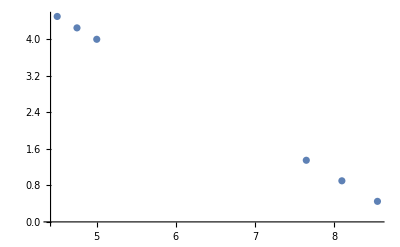

```mathematica
ListPlot[#⟦;;2⟧&/@Join[s1,s2]]
```

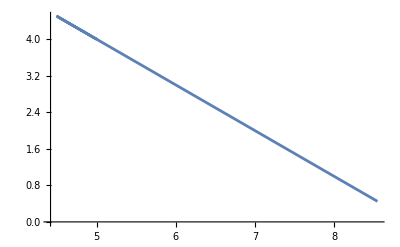

```mathematica
ListLinePlot[#⟦;;2⟧&/@Join[s1,s2]]
```

Метод равных отклонений

Уступка по первому критерию составляет 5, 10 и 15%, по второму критерию 10, 15 и 20% от соответствующих оптимальных значений.

```mathematica
ClearAll[F]
```

```mathematica
F=Subscript[g, 1];
F->max;
```

```mathematica
Maximize[Join[{
F,
Subscript[f, 1]==Subscript[g, 1],
Subscript[f, 2]==Subscript[g, 2],
Subscript[g, 1]/opt1⟦1⟧==Subscript[g, 2]/opt2⟦1⟧},
constraints],
X~Join~{Subscript[g, 1],Subscript[g, 2]}]
```

{81/14,{x_1→3/14,x_2→39/14,x_3→0,g_1→81/14,g_2→45/14}}

```mathematica
N@%
```

{5.78571,{x_1→0.214286,x_2→2.78571,x_3→0.,g_1→5.78571,g_2→3.21429}}

Метод весовых оценок

Пусть второй критерий в три раза более значим, чем первый

```mathematica
w=#/(Total@#)&@{1,3}
```

{1/4,3/4}

```mathematica
ClearAll[F]
```

```mathematica
F=w.{Subscript[f, 1]/opt1⟦1⟧,Subscript[f, 2]/opt2⟦1⟧}
```

3/20 (2 x_1+x_2-x_3)+1/36 (x_1+2 x_2+x_3)

```mathematica
Maximize[{F,constraints},X]
```

{31/36,{x_1→2,x_2→1,x_3→0}}

```mathematica
{Subscript[f, 1],Subscript[f, 2]}/.%⟦2⟧
```

{4,5}